## Backbending in nuclei

### 162Hf

```mathematica
omegaSquared={0.0271,0.0524,0.0813,0.1061,0.1219,0.0761,0.0365,0.0629,0.0858,0.1084,0.1316,0.1572,0.1856,0.1578,0.1587,0.1866,0.2167,0.2424};
moiSquared={21.0526,31.4961,39.0556,46.3464,54.6527,83.6364,141.5836,123.8266,119.6581,118.5771,118.6207,118.6270,118.4531,138.5390,148.1481,145.8840,143.9777,144.2650};
```

### 164Hf

```mathematica
omegaSquared2={0.0148,0.0376,0.0635,0.0863,0.1017,0.1199,0.0975,0.0550,0.0855,0.1147,0.1446,0.1790,0.2089,0.2394,0.2416,0.2467,0.2587,0.2779};
moiSquared2={28.4765,37.1945,44.1767,51.4051,59.8143,66.6184,86.6356,132.4503,119.8220,115.2823,113.1579,111.1768,111.6462,112.4629,120.0896,126.8882,131.7601,134.7249};
```

### 166Hf band 1

```mathematica
omegaSquared3={0.0084,0.0258,0.0466,0.0657,0.0806,0.0887,0.1045,0.0977,0.0976,0.1099,0.1334,0.1459,0.1511,0.1724,0.2000,0.1995,0.2136,0.2477};
moiSquared3={37.8215,44.8977,51.5573,58.9125,67.1972,77.4541,83.6820,99.3431,112.1615,117.7536,117.8082,123.1495,131.2572,132.5461,131.9911,141.0974,145.0216,142.7136};
```

### 166 Hf band 2

```mathematica
omegaSquared4={0.0084,0.0258,0.0466,0.0658,0.0805,0.0887,0.0494,0.0485,0.0786,0.1097,0.1367,0.1568,0.1720,0.1871,0.2054,0.2271,0.2472,0.2519};
moiSquared4={37.8310,44.8862,51.5585,58.8813,67.2328,77.4541,121.7862,140.9732,124.9554,117.8604,116.3892,118.7919,123.0547,127.2265,130.2428,132.2418,134.8089,141.5047};
```

## Plots

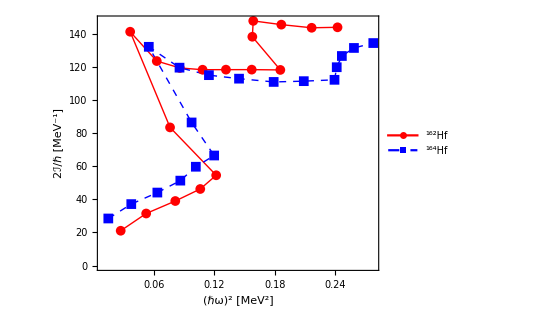

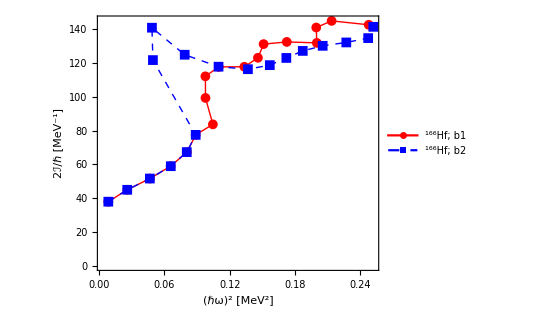

```mathematica
nucleus[name_,a_]:=Row[{Superscript["",a],name}];
p1=ListPlot[{Table[{omegaSquared[[i]],moiSquared[[i]]},{i,1,Length[omegaSquared]}],Table[{omegaSquared2[[i]],moiSquared2[[i]]},{i,1,Length[omegaSquared2]}]},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[{nucleus["Hf","162"],nucleus["Hf","164"]},Scaled[{0.8,0.3}]],LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"(ℏω)^2 [MeV^2]","2ℐ/ℏ [MeV^-1]"},ImageSize->400];
p2=ListPlot[{Table[{omegaSquared3[[i]],moiSquared3[[i]]},{i,1,Length[omegaSquared3]}],Table[{omegaSquared4[[i]],moiSquared4[[i]]},{i,1,Length[omegaSquared4]}]},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[{nucleus["Hf; b1","166"],nucleus["Hf; b2","166"]},Scaled[{0.75,0.3}]],LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"(ℏω)^2 [MeV^2]","2ℐ/ℏ [MeV^-1]"},ImageSize->400];
Show[p1]
Show[p2]
```